```mathematica
f[x_,a_,b_,c_]:=(x-a)/((b+(x-a)^c)^(1/c));
G[a_,b_,c_,ϵ_]:=(b/((1/(1-ϵ))^c-1))^(1/c)+a
```

```mathematica
a=1.54543137;
b=2.0641189;
c=0.7301633;
ϵ=0.02;
a1=-2.70;
b1=2.13;
c1=0.72;
ϵ1=0.02;
```

```mathematica
G[a,b,c,ϵ]//FullSimplify
f[G[a,b,c,ϵ],a,b,c]//FullSimplify
1-ϵ
```

861.64

0.98

0.98

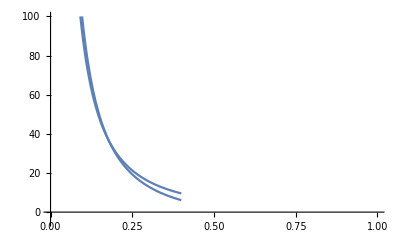

```mathematica
p1=Plot[G[a,b,c,x],{x,0,0.4},AxesOrigin->{0,0},PlotRange->{{0,1},{-5,100}}];
p2=Plot[G[a1,b1,c1,x],{x,0,0.4},AxesOrigin->{0,0},PlotRange->{{0,1},{-5,100}}];
Show[p1,p2]
```

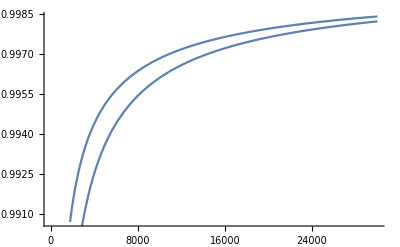

```mathematica
p1=Plot[f[x,a,b,c],{x,0,30000}];
p2 = Plot[f[x,a1,b1,c1],{x,0,30000}];
Show[p1,p2]
```

```mathematica
Manipulate[Plot[f[x,a,b,c],{x,0,xlim},AxesOrigin->{0,0}],{a,-5,5},{b,0,5},{c,0,2},{xlim,1500,10000}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 1.^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 1.^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 1.^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.